## EdgesOnTop-example.nb

Example Cellzilla2D notebook.

GPL License applies. 
See http://xlr8r.info and http://cellzilla.info for further details.

```mathematica
<<Cellzilla2D.m
```

Warning: Cellzilla2D: xSSA.m not found in path. Some stochastic conversion functions may not work as expected. It should be loaded manually before any xSSA (stochastic) simulations can be run.

Cellzilla2D (3.0.51 (05 June 2017)) loaded Tue 6 Jun 2017 12:55:03
using xCellerator 0.95 and XSSA ** Not Found **
GPL License Terms Apply

Create a tissue with a point and an edge that aren't used.

There are 8 cells in the tissue.

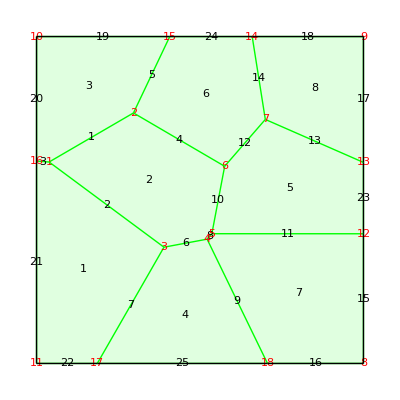

```mathematica
q=TemplateRandomSquareGrid[9, {-50, -50}, {50, 50}];
Q=Tissue2DTissue[q]; 
Print["There are ", NTissueCells[Q], " cells in the tissue."];  
ShowTissue[Q, "CellNumbers"-> True, Frame-> False, "EdgeStyles"-> Directive[Green,Thick], "EdgeNumbers"-> True, "VertexNumbers"-> Directive[Red,FontSize-> 12]]
```

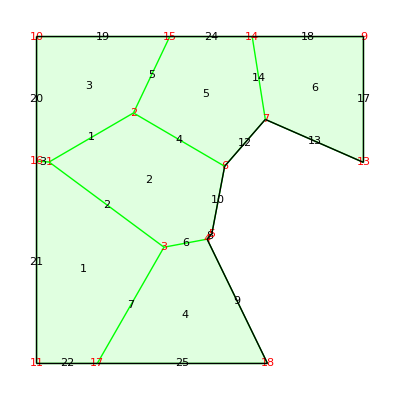

```mathematica
R=DeleteCell[Q, 5];
R=DeleteCell[R, 7];
S=DTissue2Tissue[R];
ShowTissue[S, "CellNumbers"-> True, "EdgeStyles"-> Directive[Green,Thick],"EdgeNumbers"-> True, "VertexNumbers"-> Directive[Red,FontSize-> 12]]
```

```mathematica
VerticesOnTop[S]
```

{9,14,15,10}

```mathematica
CellsOnLeft[S]
```

{1,3}

```mathematica
CellsOnBottom[S]
```

{1,4,6}

```mathematica
EdgesOnTop[S]
```

{18,19,24}

```mathematica
EdgesOnLeft[S]
```

{20,21}

```mathematica
VerticesOnLeft[S]
```

{10,16,11}

```mathematica
CellsOnBottom[S]
```

{1,4,6}